```mathematica
paso1=LaplaceTransform[x''[t]+(1.25)^2 x[t] == Sin[1.25t],t,s]
```

1.5625 LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]-s x[0]-x'[0]==1.25/(1.5625+s^2)

```mathematica
paso2=paso1/.{x[0]->0,x'[0]->0}
```

1.5625 LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]==1.25/(1.5625+s^2)

```mathematica
paso3=Solve[paso2,LaplaceTransform[x[t],t,s]]
```

{{LaplaceTransform[x[t],t,s]→1.25/((1.5625+s^2)^2)}}

```mathematica
sol=Simplify[InverseLaplaceTransform[1.25/((1.5625+s^2)^2),s,t]]//Expand
```

(0.+0.16 ⅈ) ⅇ^((0.-1.25 ⅈ) t)-(0.+0.16 ⅈ) ⅇ^((0.+1.25 ⅈ) t)-0.2 ⅇ^((0.-1.25 ⅈ) t) t-0.2 ⅇ^((0.+1.25 ⅈ) t) t

```mathematica
recta1 = Sqrt[(1.25)^2 t ^2+ 1]/(2*(1.25)^2)
```

0.32 √(1+1.5625 t^2)

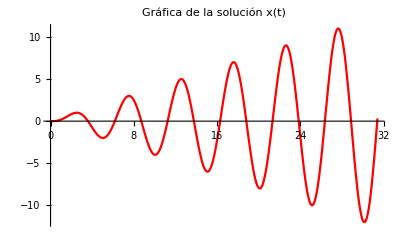

```mathematica
Plot[sol,{t,0,10Pi},PlotLabel->"Gráfica de la solución x(t)",LabelStyle->Directive[FontSize->12], PlotStyle->{Red}]
```

```mathematica
Plot[{sol,recta1, -recta1 },{t,0,10Pi},PlotStyle->{{Red,Dashing[None]}, {Blue,Dashing[None]}, {Blue,Dashing[None]}}]
```